## Solutions: Mathematica 6 Lab 3

Problem 1:

```mathematica
TrigExpand[Tan[2θ]]
TrigExpand[Cos[6θ]]
```

(2 Cos[θ] Sin[θ])/(Cos[θ]^2-Sin[θ]^2)

Cos[θ]^6-15 Cos[θ]^4 Sin[θ]^2+15 Cos[θ]^2 Sin[θ]^4-Sin[θ]^6

```mathematica
Simplify[(2 Cos[θ] Sin[θ])/(Cos[θ]^2-Sin[θ]^2)]
Simplify[Cos[θ]^6-15 Cos[θ]^4 Sin[θ]^2+15 Cos[θ]^2 Sin[θ]^4-Sin[θ]^6]
```

Tan[2 θ]

Cos[6 θ]

Problem  2:

```mathematica
TrigReduce[Sin[α]^2]
TrigReduce[Tan[θ/2]^2]
```

1/2 (1-Cos[2 α])

(1-Cos[θ])/(1+Cos[θ])

```mathematica
Simplify[1/2 (1-Cos[2 α])]
Simplify[(1-Cos[θ])/(1+Cos[θ])]
```

Sin[α]^2

Tan[θ/2]^2

Problem 3:

```mathematica
Hyperlink["MagicSquare","http://mathworld.wolfram.com/DuerersMagicSquare.html"]
```

```mathematica
M=({{16, 3, 2, 13}, {5, 10, 11, 8}, {9, 6, 7, 12}, {4, 15, 14, 1}})
```

{{16,3,2,13},{5,10,11,8},{9,6,7,12},{4,15,14,1}}

```mathematica
Tr[M]
```

34

```mathematica
Det[M]
```

0

```mathematica
Eigenvalues[M]
```

{34,-8,8,0}

```mathematica
Eigenvectors[M]
```

{{1,1,1,1},{-1,0,-1,2},{-2,1,0,1},{-1,3,-3,1}}

```mathematica
a={1,1,1,1}
b={-1,0,-1,2}
c={-2,1,0,1}
d={-1,3,-3,1}
```

{1,1,1,1}

{-1,0,-1,2}

{-2,1,0,1}

{-1,3,-3,1}

```mathematica
a.a
a.b
a.c
a.d
b.b
b.c
b.d
c.c
c.d
d.d
```

4

0

0

0

6

4

6

6

6

20

```mathematica
M.a==34a
M.b==-8 b
M.c==8c
M.d==0d
```

True

True

True

«1 more identical outputs»

Problem 4:

```mathematica
Hyperlink["LatinSquare","http://en.wikipedia.org/wiki/Latin_square"]
```

```mathematica
latin1=({{1, 2, 3, 4}, {2, 1, 4, 3}, {4, 3, 1, 2}, {3, 4, 2, 1}})
```

{{1,2,3,4},{2,1,4,3},{4,3,1,2},{3,4,2,1}}

```mathematica
Det[latin1]
```

-80

```mathematica
Eigenvalues[latin1]
```

{10,-4,-1+ⅈ,-1-ⅈ}

Problem 5:

```mathematica
latin2=({{1, 4, 2, 5, 3}, {4, 2, 5, 3, 1}, {2, 5, 3, 1, 4}, {5, 3, 1, 4, 2}, {3, 1, 4, 2, 5}})
```

{{1,4,2,5,3},{4,2,5,3,1},{2,5,3,1,4},{5,3,1,4,2},{3,1,4,2,5}}

```mathematica
Det[latin2]
```

1875

```mathematica
Eigenvalues[latin2]
```

{15,-√(25/2+(5 √5)/2),√(25/2+(5 √5)/2),-√(5/2 (5-√5)),√(5/2 (5-√5))}

```mathematica
N[%]
```

{15.,-4.25325,4.25325,-2.62866,2.62866}

Problem 6:

```mathematica
latin3=({{1, 4, 2, 5, 3}, {4, 3, 5, 3, 1}, {2, 5, 3, 1, 4}, {5, 3, 1, 4, 2}, {3, 1, 4, 2, 5}})
```

{{1,4,2,5,3},{4,3,5,3,1},{2,5,3,1,4},{5,3,1,4,2},{3,1,4,2,5}}

```mathematica
Det[latin3]
```

1900

```mathematica
Eigenvalues[latin3]
```

{Root[-1900-25 #1+375 #1^2-12 #1^3-16 #1^4+#1^5&,5],Root[-1900-25 #1+375 #1^2-12 #1^3-16 #1^4+#1^5&,4],Root[-1900-25 #1+375 #1^2-12 #1^3-16 #1^4+#1^5&,1],Root[-1900-25 #1+375 #1^2-12 #1^3-16 #1^4+#1^5&,3],Root[-1900-25 #1+375 #1^2-12 #1^3-16 #1^4+#1^5&,2]}

```mathematica
N[%]
```

{15.2107,4.26602,-3.90637,2.96105,-2.53141}

```mathematica
CharacteristicPolynomial[latin3,x]
```

1900+25 x-375 x^2+12 x^3+16 x^4-x^5

```mathematica
spectrum=x/.NSolve[%==0,x]
```

{-3.90637,-2.53141,2.96105,4.26602,15.2107}

Problem 7:

```mathematica
S=({{2, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-1, 2, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, -1, 2, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -1, 2, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -1, 2, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -1, 2, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -1, 2, -1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -1, 2, -1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -1, 2, -1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -1, 2, -1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 2, -1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 2, -1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 2, -1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 2, -1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 2, -1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 2}})
```

{{2,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,2,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,2,-1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,2,-1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,2,-1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,2,-1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-1,2,-1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,2,-1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,2,-1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,2,-1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1,2,-1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,2,-1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-1,2,-1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1,2,-1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-1,2,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,2}}

```mathematica
Eigenvalues[S]
```

{2+√(4+Root[17+204 #1+714 #1^2+1122 #1^3+935 #1^4+442 #1^5+119 #1^6+17 #1^7+#1^8&,8]),2+√(4+Root[17+204 #1+714 #1^2+1122 #1^3+935 #1^4+442 #1^5+119 #1^6+17 #1^7+#1^8&,7]),2+√(4+Root[17+204 #1+714 #1^2+1122 #1^3+935 #1^4+442 #1^5+119 #1^6+17 #1^7+#1^8&,6]),2+√(4+Root[17+204 #1+714 #1^2+1122 #1^3+935 #1^4+442 #1^5+119 #1^6+17 #1^7+#1^8&,5]),2+√(4+Root[17+204 #1+714 #1^2+1122 #1^3+935 #1^4+442 #1^5+119 #1^6+17 #1^7+#1^8&,4]),2+√(4+Root[17+204 #1+714 #1^2+1122 #1^3+935 #1^4+442 #1^5+119 #1^6+17 #1^7+#1^8&,3]),2+√(4+Root[17+204 #1+714 #1^2+1122 #1^3+935 #1^4+442 #1^5+119 #1^6+17 #1^7+#1^8&,2]),2+√(4+Root[17+204 #1+714 #1^2+1122 #1^3+935 #1^4+442 #1^5+119 #1^6+17 #1^7+#1^8&,1]),2-√(4+Root[17+204 #1+714 #1^2+1122 #1^3+935 #1^4+442 #1^5+119 #1^6+17 #1^7+#1^8&,1]),2-√(4+Root[17+204 #1+714 #1^2+1122 #1^3+935 #1^4+442 #1^5+119 #1^6+17 #1^7+#1^8&,2]),2-√(4+Root[17+204 #1+714 #1^2+1122 #1^3+935 #1^4+442 #1^5+119 #1^6+17 #1^7+#1^8&,3]),2-√(4+Root[17+204 #1+714 #1^2+1122 #1^3+935 #1^4+442 #1^5+119 #1^6+17 #1^7+#1^8&,4]),2-√(4+Root[17+204 #1+714 #1^2+1122 #1^3+935 #1^4+442 #1^5+119 #1^6+17 #1^7+#1^8&,5]),2-√(4+Root[17+204 #1+714 #1^2+1122 #1^3+935 #1^4+442 #1^5+119 #1^6+17 #1^7+#1^8&,6]),2-√(4+Root[17+204 #1+714 #1^2+1122 #1^3+935 #1^4+442 #1^5+119 #1^6+17 #1^7+#1^8&,7]),2-√(4+Root[17+204 #1+714 #1^2+1122 #1^3+935 #1^4+442 #1^5+119 #1^6+17 #1^7+#1^8&,8])}

```mathematica
N[%]
```

{3.96595,3.86494,3.70043,3.47802,3.20527,2.89148,2.54733,2.18454,1.81546,1.45267,1.10852,0.794731,0.521982,0.299566,0.135056,0.0340538}

```mathematica
CharacteristicPolynomial[%,x]
```

17-816 x+11628 x^2-77520 x^3+293930 x^4-705432 x^5+1144066 x^6-1307504 x^7+1081575 x^8-657800 x^9+296010 x^10-98280 x^11+23751 x^12-4060 x^13+465 x^14-32 x^15+x^16

```mathematica
spectrum=x/.NSolve[%==0,x]
```

{0.0340538,0.135056,0.299566,0.521982,0.794731,1.10852,1.45267,1.81546,2.18454,2.54733,2.89148,3.20527,3.47802,3.70044,3.86494,3.96595}

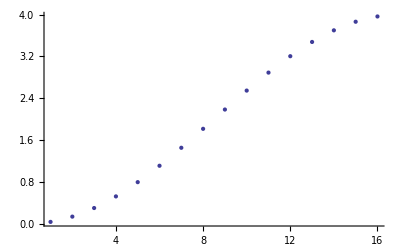

```mathematica
ListPlot[spectrum,PlotStyle->PointSize[Large]]
```

```mathematica
Subscript[S, ring]=({{2, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1}, {-1, 2, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, -1, 2, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -1, 2, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -1, 2, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -1, 2, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -1, 2, -1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -1, 2, -1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -1, 2, -1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -1, 2, -1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 2, -1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 2, -1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 2, -1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 2, -1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 2, -1}, {-1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 2}});
```

```mathematica
CharacteristicPolynomial[Subscript[S, ring],x]
```

-256 x+5440 x^2-45696 x^3+201552 x^4-537472 x^5+940576 x^6-1136960 x^7+980628 x^8-615296 x^9+283360 x^10-95680 x^11+23400 x^12-4032 x^13+464 x^14-32 x^15+x^16

```mathematica
spectrum=x/.NSolve[%==0,x]
```

{0.,0.152241,0.152241,0.585786,0.585787,1.23463,1.23463,1.99999,2.00001,2.76531,2.76542,3.41408,3.41435,3.84761,3.84791,4.}

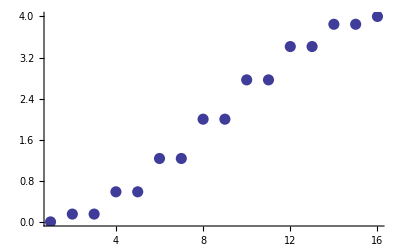

```mathematica
ListPlot[spectrum,PlotStyle->PointSize[0.02]]
```

```mathematica
Subscript[S, impure]=({{2, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-1, 2, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, -1, 2, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -1, 2, -2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -2, 3, -2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -2, 2, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -1, 2, -1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -1, 2, -1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -1, 2, -1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -1, 2, -1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 2, -1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 2, -1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 2, -1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 2, -1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 2, -1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 2}});
```

```mathematica
CharacteristicPolynomial[Subscript[S, impure],x]
```

-232+5266 x-38408 x^2+129451 x^3-210441 x^4+79583 x^5+329503 x^6-734815 x^7+812547 x^8-579582 x^9+286412 x^10-100387 x^11+24941 x^12-4299 x^13+489 x^14-33 x^15+x^16

```mathematica
spectrum=x/.NSolve[%==0,x]
```

{-0.64779,0.0787972,0.28774,0.487772,0.71514,1.08771,1.45203,1.82653,2.22619,2.55009,2.93085,3.3267,3.53224,3.71569,3.92458,5.50575}

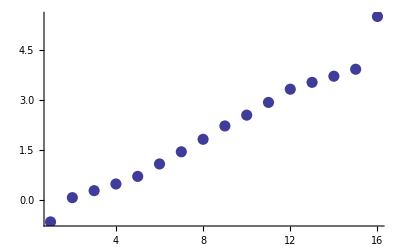

```mathematica
ListPlot[spectrum,PlotStyle->PointSize[0.02]]
```

Problem  8:

```mathematica
Needs["PhysicalConstants`"]
```

```mathematica
Needs["Units`"]
```

```mathematica
?SolarMass
?SolarRadius
?ProtonMass
?PlanckConstant
```

SolarMass is a unit of mass.

SolarRadius is a physical constant.

ProtonMass is the mass of a proton.

PlanckConstant is a universal constant of nature which relates the energy of a quantum of radiation to the frequency of the oscillator which emitted it.

```mathematica
SolarMass
SolarRadius
ProtonMass
PlanckConstant
```

SolarMass

6.9599×10^8 Meter

1.67262×10^-27 Kilogram

6.62607×10^-34 Joule Second

```mathematica
Convert[SolarMass,Kilogram]
```

1.9891×10^30 Kilogram

```mathematica
SolarMomentOfInertia=2/5(SolarMass)(SolarRadius)^2
```

1.93761×10^17 Meter^2 SolarMass

```mathematica
SolarAngularMomentum=%((2π)/(25.36Day))
```

(4.80061×10^16 Meter^2 SolarMass)/Day

```mathematica
SolarSpin=Convert[%,Kilogram Meter^2/Second]
```

(1.1052×10^42 Kilogram Meter^2)/Second

```mathematica
ProtonNumber=SolarMass/ProtonMass
```

(5.97864×10^26 SolarMass)/Kilogram

```mathematica
ProtonNumber=Convert[%,Kilogram/Kilogram]
```

1.18921×10^57

```mathematica
hbar=PlanckConstant/(2π)
```

1.05457×10^-34 Joule Second

```mathematica
TotalProtonSpin=ProtonNumber hbar/2
```

6.27054×10^22 Joule Second

```mathematica
TotalProtonSpin/SolarSpin
```

(5.67369×10^-20 Joule Second^2)/(Kilogram Meter^2)

```mathematica
Convert[ Joule Second^2,Kilogram Meter^2]
```

Kilogram Meter^2